# Hückel Theory:

```mathematica
Clear[x,α, β]
α=0; β=1; (* Able to have numerical analysis. 
             * Some issues(bugs) with Mathematica  
             * analytical solver.                   *)
```

Heteroatom parameters in Hückel Theory
https://www.chem.tamu.edu/rgroup/hughbanks/courses/673/handouts/Huckel_Heteroatom_parameters.pdf

## 1. Ethylene

{-1,1}

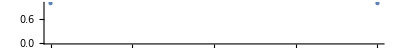

```mathematica
result=α -β x /.Solve[{Det[{{x, 1}, {1, x}}]==0}, x]//Sort
NumberLinePlot[result, ImageSize->Tiny]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+1]]-result[[#]]& @@ {Length[result]/2}
```

2

## 2. 1,3-butadiene

{1/2 (-1-√5),1/2 (1-√5),1/2 (-1+√5),1/2 (1+√5)}

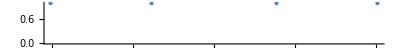

```mathematica
result=α -β x /.Solve[{Det[{{x, 1, 0, 0}, {1, x, 1, 0}, {0, 1, x, 1}, {0, 0, 1, x}}]==0}, x]//Sort
NumberLinePlot[result, ImageSize->Tiny]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+1]]-result[[#]]& @@ {Length[result]/2}//N
```

1.23607

E_stab=E_total-E_n: (in unit of β)

```mathematica
2 (-#-Plus@@Take[result,#])&@@{Length[result]/2}//N
```

0.472136

## 3. cyclobutadiene

{-2,0,0,2}

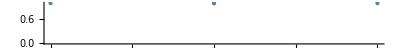

```mathematica
result=α -β x /.Solve[{Det[{{x, 1, 0, 1}, {1, x, 1, 0}, {0, 1, x, 1}, {1, 0, 1, x}}]==0},x] //Sort
NumberLinePlot[result, ImageSize->Tiny]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+2]]-result[[#]]& @@ {Length[result]/2}//N
```

2.

E_stab=E_total-E_n: (in unit of β)

```mathematica
2 (-#-Plus@@Take[result,#])&@@{Length[result]/2}//N
```

0.

## 4. benzene

{-2,-1,-1,1,1,2}

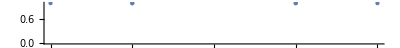

```mathematica
result=α -β x /.Solve[{Det[{{x, 1, 0, 0, 0, 1}, {1, x, 1, 0, 0, 0}, {0, 1, x, 1, 0, 0}, {0, 0, 1, x, 1, 0}, {0, 0, 0, 1, x, 1}, {1, 0, 0, 0, 1, x}}]==0}, x] //Sort
NumberLinePlot[result, ImageSize->Tiny]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+1]]-result[[#]]& @@ {Length[result]/2}//N
```

2.

E_stab=E_total-E_n: (in unit of β)

```mathematica
2 (-#-Plus@@Take[result,#])&@@{Length[result]/2}//N
```

2.

## 5. pyridine

{-1.95432,-1.06177,-1.,0.667312,1.,1.84878}

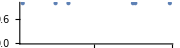

```mathematica
result=e /.Solve[{Det[{{α-e-0.5β, 0.8β, 0, 0, 0, 0.8β}, {0.8 β, α-e, β, 0, 0, 0}, {0, β, α-e, β, 0, 0}, {0, 0, β, α-e, β, 0}, {0, 0, 0, β, α-e, β}, {0.8 β, 0, 0, 0, β, α-e}} ]==0}, e] //Sort
(* Inversing values to show numbers on left side, thus the hight of each
* Level are correct, but values are negatived. 
 *)
NumberLinePlot[Map[-#&,result], ImageSize->Small]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+1]]-result[[#]]& @@ {Length[result]/2}//N
```

1.66731

## 6. Naphthalene

{-2.30278,-1.61803,-1.30278,-1.,-0.618034,0.618034,1.,1.30278,1.61803,2.30278}

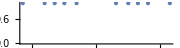

```mathematica
result=α -β x /. NSolve[{Det[{{x, 1, 0, 0, 0, 1, 0, 0, 0, 0}, {1, x, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, x, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, x, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, x, 1, 0, 0, 0, 1}, {1, 0, 0, 0, 1, x, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, x, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, x, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1, x, 1}, {0, 0, 0, 0, 1, 0, 0, 0, 1, x}} ]==0}, x]//Sort
NumberLinePlot[result, ImageSize->Small]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+1]]-result[[#]]& @@ {Length[result]/2}//N
```

1.23607

E_stab=E_total-E_n: (in unit of β)

```mathematica
2 (-#-Plus@@Take[result,#])&@@{Length[result]/2}//N
```

3.68324

## 7. Biphenyl

{-2.27841,-1.89122,-1.31743,-1.,-1.,-0.704624,0.704624,1.,1.,1.31743,1.89122,2.27841}

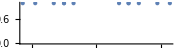

```mathematica
result=α -β x /.NSolve[{Det[{{x, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {1, x, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, x, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, x, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, x, 1, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 1, x, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, x, 1, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 1, x, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, x, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, x, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, x, 1}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, x}} ]==0}, x] //Sort
NumberLinePlot[result, ImageSize->Small]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+1]]-result[[#]]& @@ {Length[result]/2}//N
```

1.40925

E_stab=E_total-E_n: (in unit of β)

```mathematica
2 (-#-Plus@@Take[result,#])&@@{Length[result]/2}//N
```

4.38338

## 8. 2,2’-bipyridine

{-2.21147,-1.85832,-1.31771,-1.05247,-1.04884,-0.752641,0.437626,0.755867,0.86986,1.31301,1.77053,2.09455}

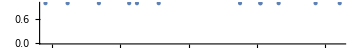

```mathematica
result=e /.NSolve[{Det[
{{α-e, β, 0, 0, 0, β, 0, 0, 0, 0, 0, 0}, {β, α-e, β, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, β, α-e, β, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, β, α-e, 0.8β, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0.8β, α-e-0.5β, 0.8β, 0, 0, 0, 0, 0, 0}, {β, 0, 0, 0, 0.8β, α-e, β, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, β, α-e, 0.8β, 0, 0, 0, β}, {0, 0, 0, 0, 0, 0, 0.8β, α-e-0.5β, 0.8β, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0.8β, α-e, β, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, β, α-e, β, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, β, α-e, β}, {0, 0, 0, 0, 0, 0, β, 0, 0, 0, β, α-e}}
 ]==0}, e] //Sort
(* Inversing values to show numbers on left side, thus the hight of each
* Level are correct, but values are negatived. 
 *)
NumberLinePlot[Map[-#&,result], ImageSize->Medium]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+1]]-result[[#]]& @@ {Length[result]/2}//N
```

1.19027

## 9. Phenanthrene

{-2.43476,-1.95063,-1.51627,-1.3058,-1.14238,-0.769052,-0.605225,0.605225,0.769052,1.14238,1.3058,1.51627,1.95063,2.43476}

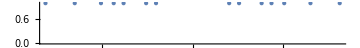

```mathematica
result=α -β x /.NSolve[{Det[{{x, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, x, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, x, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, x, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, x, 1, 0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 1, x, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, x, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, x, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, x, 1, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0, 0, 0, 1, x, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, x, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, x, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, x, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, x}} ]==0}, x] //Sort
NumberLinePlot[result, ImageSize->Medium]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+1]]-result[[#]]& @@ {Length[result]/2}//N
```

1.21045

E_stab=E_total-E_n: (in unit of β)

```mathematica
2 (-#-Plus@@Take[result,#])&@@{Length[result]/2}//N
```

5.44825

## 10. Phenanthroline

{-2.31885,-1.76943,-1.55844,-1.34375,-1.,-0.926156,-0.478117,0.276447,0.524948,1.,1.2133,1.4952,1.63782,2.24703}

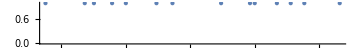

```mathematica
result=e /.NSolve[{Det[
{{α-e, β, 0, 0, 0, β, 0, 0, 0, 0, 0, 0, 0, 0}, {β, α-e, β, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, β, α-e, 0.8β, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0.8β, α-e-0.5β, 0.8β, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0.8β, α-e, β, 0, 0, 0, β, 0, 0, 0, 0}, {β, 0, 0, 0, β, α-e, β, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, β, α-e, β, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, β, α-e, β, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, β, α-e, β, 0, 0, 0, 0}, {0, 0, 0, 0, β, 0, 0, 0, β, α-e, 0.8β, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0.8β, α-e-0.5β, 0.8β, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.8β, α-e, β, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, β, α-e, β}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, β, α-e}} 
]==0}, e] //Sort
NumberLinePlot[Map[-#&,result], ImageSize->Medium]//Rotate[#,-π/2]&
```

ΔE = E_HOMO- E_LUMO: (in unit of β)

```mathematica
result[[#+1]]-result[[#]]& @@ {Length[result]/2}//N
```

0.754565